ⅇ^(-(a (-sint x+cost y)^2)/B^2) p0 (1-(cb (-sint x+cost y)^2)/B^2) (1-(cl (cost x+sint y)^4)/L^4)

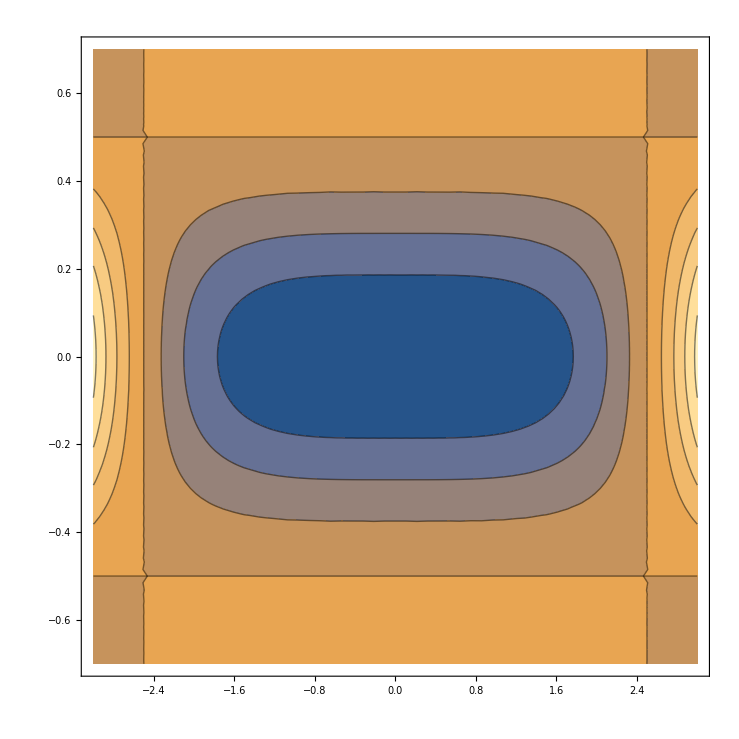

```mathematica
ϵ=cost*x+sint*y;
η=-sint*x+cost*y;
pr=p0*(1-cl*(ϵ^4/L^4))*(1-cb*(η^2/B^2))*Exp[-a*(η^2/B^2)]
prDx=Simplify[D[pr,x]];
prDy=Simplify[D[pr,y]];
prv=-1*(1-16*(x^4/5^4))*(1-4*(y^2/1^2))*Exp[-4*(y^2/1^2)];
(*Plot3D[prv,{x,-3,3},{y,-1.5,1.5}]*)
ContourPlot[prv,{x,-3,3},{y,-0.7,0.7}]
```